```mathematica
fiberDens = 892; (*kg/m^3*)
boatDens = 1.225*(1.875/2)+fiberDens*(.125/2) ;(*Boat density (kg/m^3)*)
deckDens = fiberDens* 0.003175 ;(*Deck area density (kg/m^2*)
mCargo = .8; (*Cargo mass (kg)*)
mMast = (π*(3/8*1/2)^2*19.685*(2.7/0.0610237))/1000; (*Mass of mast (kg)*)
mDeck = deckDens*RegionMeasure[ImplicitRegion[boatFunc[a,b,c,x,.1],{x,y}]];
comMast = {0,0,.31}; (*COM of mast (m)*)
comCargo = {0,0,.041}; 
comDeck = {0,0,b-0.0015875};
a=.65;(*Curviness of dat boat*)
b=.17;(*height of boat (m)*)
c=.25;(*xLen/2 of boat (m)*)
(*COM of cargo (m)*)
```

```mathematica
Clear[boat,mass,com,submerged,submass,water,cob,arm]
boatFunc[n_?NumberQ,d_?NumberQ,xLen_?NumberQ,xVal_,zVal_]:=2*Abs[y/n]^1.5+d*(xVal^2/xLen^2)≤zVal≤d
boatSlice[n_?NumberQ,d_?NumberQ,xLen_?NumberQ,xVal_]:=2*Abs[y/n]^1.5+d*(xVal^2/xLen^2)==z
boatFuncCurve[n_?NumberQ,d_?NumberQ,xLen_?NumberQ,xVal_,zVal_?NumberQ]:=2*Abs[y/n]^1.5+d*(xVal^2/xLen^2)==zVal
boatFuncY[d_?NumberQ,xLen_?NumberQ,xVal_]:=d*(xVal^2/xLen^2)==z
boat= ImplicitRegion[boatFunc[a,b,c,x,z] ,{x,y,z}];
mass :=mass= boatDens*N[RegionMeasure[boat]]
massTot:=mass+mCargo+mMast+mDeck
com:=com=(N[RegionCentroid[boat]]*mass+mCargo*comCargo+mMast*comMast+comDeck*mDeck)/massTot
submerged[d_,t_]:=boatFunc[a,b,c,x,z]&&If[t<90,z<N[Tan[t Degree]]*y+d,z>N[Tan[t Degree]]*y+d]
submass[d_,t_]:=submass[d,t]=1000*N[RegionMeasure[ImplicitRegion[submerged[d,t],{x,y,z}]]]
water[t_]:=water[t]=FindRoot[submass[d,t]==massTot,{d,-20,20}]
cob[t_]:=cob[t]=N[RegionCentroid[ImplicitRegion[submerged[d,t]/.water[t],{x,y,z}]]]
arm[t_?NumberQ]:=Cross[cob[t]-com,{0,-Sin[t Degree]*9.81submass[d,0]/.water[0],Cos[t Degree]*9.81submass[d,0]/.water[0]}][[1]]
```

```mathematica
RegionBounds[ImplicitRegion[boatFunc[a,b,c,x,z],{x,y,z}]]
```

```mathematica
boatFuncY[b,c,x]
```

```mathematica
Solve[boatFuncCurve[a,b,c,x,.17-.003175],y]
```

```mathematica
N@Tan[0]//AbsoluteTiming
N@Tan[120Degree]//AbsoluteTiming
```

```mathematica
Table[boatSlice[a,b,c,i],{i,-c+0.05,c-0.05,.05}]
```

{0.1088+3.81645 Abs[y]^1.5==z,0.0612+3.81645 Abs[y]^1.5==z,0.0272+3.81645 Abs[y]^1.5==z,0.0068+3.81645 Abs[y]^1.5==z,0.+3.81645 Abs[y]^1.5==z,0.0068+3.81645 Abs[y]^1.5==z,0.0272+3.81645 Abs[y]^1.5==z,0.0612+3.81645 Abs[y]^1.5==z,0.1088+3.81645 Abs[y]^1.5==z}

{120,140}

ImplicitRegion::msgs: Evaluation of {submerged[d,120]/.water[120],True} generated message(s) {RegionMeasure::nmet}.

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[3.81645 Abs[y]^1.5+2.72 x^2≤z≤0.17&&z<0.+d,{x,y,z}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

ImplicitRegion::msgs: Evaluation of {submerged[d,140]/.water[140],True} generated message(s) {RegionMeasure::nmet}.

{{120,0.148619},{140,-0.148202}}

0.976189-0.0000867729 x-0.0000567471 x^2

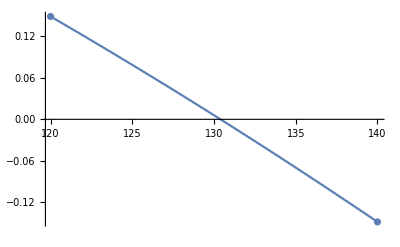

```mathematica
(*angles = Range[120,140,10]*)
angles = {120,140}
data  = Map[arm,angles];
data2 = Transpose[{angles,data}]
line = Fit[data2,{1,x,x^2},x]
Show[ListPlot[data2],Plot[line,{x,120,140}]]
```

```mathematica
data2 = Transpose[{{120,140},{1,2}}]
```

```mathematica
Manipulate[RegionPlot3D[boatFunc[d,e,f,x,z],{x,-.5,.5},{y,-.2,.2},{z,0,.17},AxesLabel->Automatic,BoxRatios->Automatic],{d,.75,1},{e,.11,.17},{f,.25,.5}]
```

```mathematica
points = Map[arm,Range[120,140,5]]
angles = Range[120,140,5]
newPoints = Transpose[{angles,points}]
ListPlot[newPoints]
```

```mathematica
ClearAll[sliceBoat]
prisCoeff:=RegionMeasure[ImplicitRegion[submerged[d,0]/.water[0],{x,y,z}]]/(RegionMeasure[ImplicitRegion[boatFunc[a,b,c,0,z]&&z<d/.water[0],{y,z}]]*2RegionBounds[ImplicitRegion[submerged[d,0]/.water[0],{x,y,z}]][[1,2]])
```

```mathematica
prisCoeff
```

```mathematica
RegionPlot[boatFunc[.75,.1,.25,0,z],{y,-.1,.1},{z,0,.1}]
```